```mathematica
Nt = 551;
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx =551; 
(*xi = -2; xf = 8;*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx;
c =  1;
r = c * (deltat / deltax)//N
```

0.159155

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
```

```mathematica
T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1}],32];

(*For Perodic Interpolation*) 
Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

X= N[Table[xm = xi + m *deltax, {m, 0, Nx - 1}],32];

f[x_] =ⅇ^(- 8(x-π)^2);
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrices*)
(************************************************************************************************************************)
```

```mathematica
L11 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L11//MatrixForm;
DL11 = N[-c * L11 * deltat,32];

L12 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL12 = N[-c * L12 * deltat,32];

L22 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL22 = N[(-c)^2 * L22 * (deltat)^2,32];

L14 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L14//MatrixForm;
DL14 = N[-c * L14 * deltat,32];

L24 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L24//MatrixForm;
DL24 = N[(-c)^2 * L24 * (deltat)^2,32];

L34 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[3],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL34 = N[(-c)^3 * L34 * (deltat)^3,32];

L44 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[4],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL44 = N[(-c)^4 * L44 * (deltat)^4,32];
```

```mathematica
(*LD2*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]


I1 = N[IdentityMatrix[Length[DL12]],32];
A = N[I1 - ((DL12 / 2)),32];
B = N[I1 + ((DL12 / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCN[[n+1,All]] = UCN[[n,All]] + (EMCN).UCN[[n,All]], {n,1,Nt - 1 }];
```

5.1225022792354301755235586765003×10^-35

True

```mathematica
(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = Chop[URK2, 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = N[IdentityMatrix[Length[DL12]],32];

MRK2 = N[(IRK2 + (DL12) + ((1/2)*(DL22))),32];

EMRK2 = N[MRK2 - IRK2,32];

EMRK2 = Developer`ToPackedArray[EMRK2, Real]; 

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

5.1225022792354301755235586765003×10^-35

True

1.

0.9746697040894155571390301341976

-0.0253302959105844428609698658024

```mathematica
(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = Chop[URK4, 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = N[IdentityMatrix[Length[DL14]],32];

MRK4 = N[IRK4 + DL14 + ((1/2) * (DL24)) + ((1/6) * (DL34)) + ((1/24) * (DL44)),32];

EMRK4 = N[MRK4 - IRK4,32];

EMRK4 = Developer`ToPackedArray[EMRK4, Real]; 

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD4*)
UN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UN[[1,All]] = N[f[X],32];
UN = Chop[UN, 10^(-307)];
UN [[1,1]]
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]


IN = N[IdentityMatrix[Length[DL14]],32];
AN = N[IN - ((DL14 / 2)) + (((DL24)/12)),32];
BN = N[IN + ((DL14 / 2)) + (((DL24)/12)),32];
MN = N[Inverse[AN].BN,32];
EMN = N[MN - IN,32];

EMN = Developer`ToPackedArray[EMN, Real]; 

Do[UN[[n+1,All]] = UN[[n,All]] + (EMN).UN[[n,All]], {n,1,Nt - 1 }]
```

5.1225022792354301755235586765003×10^-35

True

1.

0.9947228550186282410706312779578

0.9947228550186282410706312779578

0.9885346345132087711995654745421

-0.011465365486791228800434525458

```mathematica
(*Don't need the Differentiation Matrices to have 32 digits anymore*)
{{L11 = Developer`ToPackedArray[L11, Real]; 
L12 = Developer`ToPackedArray[L12, Real]; 
L22 = Developer`ToPackedArray[L22, Real]; 
L14 = Developer`ToPackedArray[L14, Real]; 
L24 = Developer`ToPackedArray[L24, Real];
L34 = Developer`ToPackedArray[L34, Real];}, {L44 = Developer`ToPackedArray[L44, Real];}}
```

{{Null^6},{Null}}

```mathematica
(************************************************************************************************************************)
(* Eigenvalues*)
(************************************************************************************************************************)
```

```mathematica
(*CN*)
(*evals = Eigenvalues[N[MCN]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK2*)
(*evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*RK4*)
(*evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(*LD4*)
(*evalsN = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];
Do[
FCN[[i,All]] = (L12.UCN[[i,All]])^2;

intCN[[i]] = (xf - xi)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intCN}]},Joined->True]*)
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
FRK2 = Developer`ToPackedArray[FRK2, Real];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = Developer`ToPackedArray[intRK2, Real];
Do[
FRK2[[i]] = (L12.URK2[[i,All]])^2;

intRK2[[i]] = (xf-xi)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
FRK4 = Developer`ToPackedArray[FRK4, Real];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = Developer`ToPackedArray[intRK4, Real];
Do[
FRK4[[i]] = (L14.URK4[[i,All]])^2;

intRK4[[i]] = (xf-xi)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},Joined->True]*)
```

```mathematica
(*LD4*)
FN = Table[0,{i,1,Nt},{j,1,Nx}];
FN = Developer`ToPackedArray[FN, Real];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
intN = Developer`ToPackedArray[intN, Real];
Do[
FN[[i]] = (L14.UN[[i,All]])^2;

intN[[i]] = (xf-xi)/Nx Total[FN[[i,All]]]
,{i,1,Length[FN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intN}]},Joined->True]*)
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD4 = Abs[intN - intN[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
```

```mathematica
(*ListLinePlot[{Transpose[{T,energyErrorLD2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorLD4}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK2}]},Joined->True,PlotRange->All]
ListLinePlot[{Transpose[{T,energyErrorRK4}]},Joined->True,PlotRange->All]*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

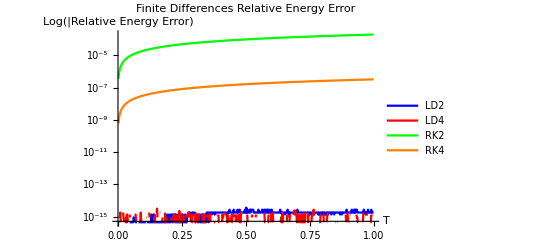

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotStyle->{Blue, Red,Green, Orange},PlotLegends->{"LD2","LD4","RK2","RK4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Finite Differences Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error.dat",exportData,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*L1 Error*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = ⅇ^(- 8((x - t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}]]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
errorRK2 = Developer`ToPackedArray[errorRK2, Real];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

```mathematica
(*LD4*)
abserrLD4 = Abs[UN-Uexact];
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
errorLD4 = Developer`ToPackedArray[errorLD4, Real];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
errorRK4 = Developer`ToPackedArray[errorRK4, Real];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}]]*)
```

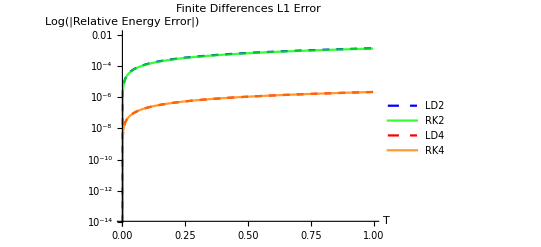

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}]},PlotRange->{{ti,tf},{10^(-14),10^(-2)}}, PlotStyle->{{Blue,Dashed},{Green,Opacity[0.8]},{Red,Dashed},{Orange,Opacity[0.8]}},PlotLabel->"Finite Differences L1 Error",PlotLegends->{"LD2","RK2","LD4","RK4"},AxesLabel->{"T","Log(|Relative Energy Error|)"},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_FD.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
(********************************************************************************************************************)
(*Start/Final*)
(********************************************************************************************************************)
```

```mathematica
(*LD2*)
LD2start = UCN[[1]];
LD2startErr = UCN[[1]] - Uexact[[1]];
LD2end = Last[UCN];
LD2endErr = Last[UCN] - Last[Uexact];

(*LD4*)
LD4start = UN[[1]];
LD4startErr = UN[[1]] - Uexact[[1]];
LD4end = Last[UN];
LD4endErr = Last[UN] - Last[Uexact];

(*RK2*)
RK2start = URK2[[1]];
RK2startErr = URK2[[1]] - Uexact[[1]];
RK2end = Last[URK2];
RK2endErr = Last[URK2] - Last[Uexact];

(*RK4*)
RK4start = URK4[[1]];
RK4startErr = URK4[[1]] - Uexact[[1]];
RK4end = Last[URK4];
RK4endErr = Last[URK4] - Last[Uexact];

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final.dat",exportData,"Table"];*)
```

```mathematica
aniexact = Animate[Plot[ⅇ^(- 4((x - t)-π)^2),{x,xi,xf},PlotRange->{{xi,xf},{0,1}}],{t,ti,tf}]
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,UCN[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{xi,xf},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,Abs[UCN[[n]] - Uexact[[n]]]}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```